## Check for k=2, M=1, N=0 (ok) [7 Feb 2021]

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=2;
mM=1;
```

```mathematica
nmax=0;
```

```mathematica
Table[(
ell[r]=mM+1/2-r;
),{r,1,mM}];
Table[(
H11rs[n]=Import[StringJoin["210202_H11rsn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H13sr[n]=Import[StringJoin["210202_H13srn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H14primesr[n]=Import[StringJoin["210202_H14primesrn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H12primers[n]=Import[StringJoin["210202_H12primersn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H22primeprimesr[n]=Import[StringJoin["210202_H22primeprimesrn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H24primeprimesr[n]=Import[StringJoin["210202_H24primeprimesrn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
),{n,0,nmax}];
```

```mathematica
(*M=1の場合各成分はr,sの添字について1x1なので, 転置は無視して良い*)
matH11=Sum[H11rs[n]*z^n,{n,0,nmax}];
matH12=Sum[H12primers[n]*z^n,{n,0,nmax}];
matH13=Sum[H13sr[n]*z^n,{n,0,nmax}];
matH14=1/(√(2*I*k))*Exp[-(π*I)/(2*k)*(mM-ell[1]-ell[1])^2]+Sum[H14primesr[n]*z^(n+1),{n,0,nmax-1}];
matH21=-matH12;
matH22=Sum[H22primeprimesr[n]*z^(n+1),{n,0,nmax-1}];
matH23=Conjugate[matH14];
matH24=Sum[H24primeprimesr[n]*z^(n+1),{n,0,nmax-1}];
matH31=-matH13;
matH32=-Conjugate[matH14];
matH33=Normal[Series[z*Conjugate[matH11],{z,0,nmax}]];
matH34=Normal[Series[z*Conjugate[matH12],{z,0,nmax}]];
matH41=-matH14;
matH42=-matH24;
matH43=Normal[Series[-z*Conjugate[matH12],{z,0,nmax}]];
matH44=Normal[Series[z*Conjugate[matH22],{z,0,nmax}]];
```

```mathematica
matH={{matH11,matH12,matH13,matH14},
{matH21,matH22,matH23,matH24},
{matH31,matH32,matH33,matH34},
{matH41,matH42,matH43,matH44}};
```

```mathematica
MatrixForm[matH//ComplexExpand]
```

(-(1/128+ⅈ/128)/(√2) | -ⅈ/8 | -1/8 | (1/2-ⅈ/2)/(√2)
ⅈ/8 | 0 | (1/2+ⅈ/2)/(√2) | 0
1/8 | -(1/2+ⅈ/2)/(√2) | 0 | 0
-(1/2-ⅈ/2)/(√2) | 0 | 0 | 0)

```mathematica
sqrtdet2=Normal[Series[√Normal[Series[(Det[matH]//ComplexExpand),{z,0,nmax}]],{z,0,nmax}]];
```

```mathematica
(**)
(*sqrtdet2=√Subscript[detH, ij,rs]*)
(**)
```

```mathematica
sqrtdet2=Collect[(sqrtdet2//Expand),z]
```

1/4

```mathematica
(**)
(*Direct calculation*)
(**)
```

```mathematica
Det[{{(-1)^mM/(4*k)*Exp[-(π*I)/(2*k)*((mM+1/2-1)^2-(mM+1/2-1)^2)]/Cos[(π*(mM+1/2-1-(mM+1/2-1)))/(2*k)],1/(√(2*I*k))*Exp[-(π*I)/(2*k)*(mM+1/2-1+mM+1/2-1-mM)^2]},
{√(I/(2*k))*Exp[(π*I)/(2*k)*(mM+1/2-1+mM+1/2-1-mM)^2],0}}]
```

-1/4

## Check for k=2, M=1, N=1,2,3 (not ok) [7 Feb 2021]

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=2;
mM=1;
```

```mathematica
nmax=3;
```

```mathematica
Table[(
trρ[n]=Import[StringJoin["../210122_TWPY_M0_withtrrhoevensymmetrized/k",ToString[k],"_server/210120_trrho_k",ToString[k],"_n",ToString[n],".m"]]//Expand;
),{n,1,nmax}];
```

```mathematica
(**)
(*
Subscript[Σ, N] z^N*Z(N)=Ξ(z)=Exp[1/2 Tr[Log[1+zρ]]]=Subscript[Σ, n] e^(J(μ+2πin)),
J=C/3 μ^3+Bμ+A+O(e^(-(...)μ))
*)
(**)
```

```mathematica
Clear[f];
sqrtdet1=Normal[Series[Exp[1/2*Sum[(-1)^(n-1)/n*z^n*(-1)^(mM*n)*f[n],{n,1,7}]],{z,0,nmax}]];
```

```mathematica
Table[(
f[n]=trρ[n];
),{n,1,nmax}];
```

```mathematica
(**)
(*sqrtdet1=√(det(1+zρ))*)
(**)
```

```mathematica
sqrtdet1=Collect[(sqrtdet1//Expand),z]
```

1-z/128+(35/262144-1/(768 π^2)) z^2+(-313/33554432+1/(98304 π^2)+41/(1572864 π)) z^3

```mathematica
Table[(
ell[r]=mM+1/2-r;
),{r,1,mM}];
Table[(
H11rs[n]=Import[StringJoin["210202_H11rsn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H13sr[n]=Import[StringJoin["210202_H13srn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H14primesr[n]=Import[StringJoin["210202_H14primesrn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H12primers[n]=Import[StringJoin["210202_H12primersn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H22primeprimesr[n]=Import[StringJoin["210202_H22primeprimesrn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
H24primeprimesr[n]=Import[StringJoin["210202_H24primeprimesrn_k2_r1_s1_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;
),{n,0,nmax}];
```

```mathematica
(*M=1の場合各成分はr,sの添字について1x1なので, 転置は無視して良い*)
matH11=Sum[H11rs[n]*z^n,{n,0,nmax}];
matH12=Sum[H12primers[n]*z^n,{n,0,nmax}];
matH13=Sum[H13sr[n]*z^n,{n,0,nmax}];
matH14=1/(√(2*I*k))*Exp[-(π*I)/(2*k)*(mM-ell[1]-ell[1])^2]+Sum[H14primesr[n]*z^(n+1),{n,0,nmax-1}];
matH21=-matH12;
matH22=Sum[H22primeprimesr[n]*z^(n+1),{n,0,nmax-1}];
matH23=Conjugate[matH14];
matH24=Sum[H24primeprimesr[n]*z^(n+1),{n,0,nmax-1}];
matH31=-matH13;
matH32=-Conjugate[matH14];
matH33=Normal[Series[z*Conjugate[matH11],{z,0,nmax}]];
matH34=Normal[Series[z*Conjugate[matH12],{z,0,nmax}]];
matH41=-matH14;
matH42=-matH24;
matH43=Normal[Series[-z*Conjugate[matH12],{z,0,nmax}]];
matH44=Normal[Series[z*Conjugate[matH22],{z,0,nmax}]];
```

```mathematica
matH={{matH11,matH12,matH13,matH14},
{matH21,matH22,matH23,matH24},
{matH31,matH32,matH33,matH34},
{matH41,matH42,matH43,matH44}};
```

```mathematica
MatrixForm[matH//ComplexExpand]
```

(-1/(128 √2)+(9 z)/(65536 √2)-(19 z)/(30720 √2 π)-(1169 z^2)/(134217728 √2)-(43 z^2)/(2949120 √2 π^2)+(481 z^2)/(15728640 √2 π)+(9023 z^3)/(34359738368 √2)+(67 z^3)/(424673280 √2 π^3)-(6313 z^3)/(7549747200 √2 π^2)-(13073063 z^3)/(22323092520960 √2 π)+ⅈ (-1/(128 √2)-(17 z)/(65536 √2)+(19 z)/(30720 √2 π)-(1585 z^2)/(134217728 √2)-(43 z^2)/(2949120 √2 π^2)+(211 z^2)/(5242880 √2 π)-(18979 z^3)/(34359738368 √2)-(67 z^3)/(424673280 √2 π^3)+(1531 z^3)/(2516582400 √2 π^2)+(6903451 z^3)/(4464618504192 √2 π)) | z/512-(47 z)/(6144 π)+(311 z^2)/3145728+(7 z^2)/(1048576 π)-(769 z^3)/1073741824-(593 z^3)/(47185920 π^2)+(837469 z^3)/(96636764160 π)+ⅈ (-1/8-(3953 z)/2949120-z/(256 π^2)+(303 z^2)/16777216+(169 z^2)/(491520 π)+(1779 z^3)/34359738368+(31 z^3)/(5734400 π^2)+(989 z^3)/(1006632960 π)) | -1/8-(7 z)/8192-(91 z^2)/1048576+(31 z^2)/(122880 π)-(6045 z^3)/4294967296+z^3/(819200 π^2)+(61 z^3)/(15728640 π) | 1/(2 √2)+z/(1024 √2)-z/(256 √2 π^2)+(5 z)/(384 √2 π)+(137 z^2)/(1048576 √2)+z^2/(196608 √2 π^4)-z^2/(24576 √2 π^3)-(67 z^2)/(393216 √2 π^2)-(29 z^2)/(122880 √2 π)+(1655 z^3)/(1073741824 √2)-z^3/(377487360 √2 π^6)+(13 z^3)/(188743680 √2 π^5)-(475 z^3)/(905969664 √2 π^4)-(30283 z^3)/(6794772480 √2 π^3)-(8296367 z^3)/(1902536294400 √2 π^2)-(666413 z^3)/(317089382400 √2 π)+ⅈ (-1/(2 √2)-(7 z)/(1024 √2)+z/(256 √2 π^2)+z/(192 √2 π)-(97 z^2)/(1048576 √2)-z^2/(196608 √2 π^4)-z^2/(16384 √2 π^3)-(29 z^2)/(131072 √2 π^2)+(149 z^2)/(589824 √2 π)-(8509 z^3)/(1073741824 √2)+z^3/(377487360 √2 π^6)+z^3/(18874368 √2 π^5)-(539 z^3)/(905969664 √2 π^4)+(6835 z^3)/(1358954496 √2 π^3)+(4703687 z^3)/(1902536294400 √2 π^2)+(144245 z^3)/(6341787648 √2 π))
-z/512+(47 z)/(6144 π)-(311 z^2)/3145728-(7 z^2)/(1048576 π)+(769 z^3)/1073741824+(593 z^3)/(47185920 π^2)-(837469 z^3)/(96636764160 π)+ⅈ (1/8+(3953 z)/2949120+z/(256 π^2)-(303 z^2)/16777216-(169 z^2)/(491520 π)-(1779 z^3)/34359738368-(31 z^3)/(5734400 π^2)-(989 z^3)/(1006632960 π)) | (11 z)/(4096 √2)-z/(256 √2 π^2)-z/(192 √2 π)+(73 z^2)/(4194304 √2)+z^2/(196608 √2 π^4)-(97 z^2)/(1572864 √2 π^2)-(1343 z^2)/(5898240 √2 π)+(33901 z^3)/(12884901888 √2)-z^3/(377487360 √2 π^6)-(17 z^3)/(94371840 √2 π^5)-(7537 z^3)/(3623878656 √2 π^4)+(5227 z^3)/(6794772480 √2 π^3)-(41219543 z^3)/(7610145177600 √2 π^2)-(992989 z^3)/(211392921600 √2 π)+ⅈ ((13 z)/(4096 √2)+z/(256 √2 π^2)-(5 z)/(384 √2 π)+(3593 z^2)/(12582912 √2)-z^2/(196608 √2 π^4)-z^2/(49152 √2 π^3)+(1001 z^2)/(1572864 √2 π^2)+(1711 z^2)/(3932160 √2 π)-(36457 z^3)/(12884901888 √2)+z^3/(377487360 √2 π^6)-(37 z^3)/(188743680 √2 π^5)+(13897 z^3)/(3623878656 √2 π^4)+(53515 z^3)/(2717908992 √2 π^3)-(143969797 z^3)/(7610145177600 √2 π^2)+(31837783 z^3)/(1268357529600 √2 π)) | 1/(2 √2)+z/(1024 √2)-z/(256 √2 π^2)+(5 z)/(384 √2 π)+(137 z^2)/(1048576 √2)+z^2/(196608 √2 π^4)-z^2/(24576 √2 π^3)-(67 z^2)/(393216 √2 π^2)-(29 z^2)/(122880 √2 π)+(1655 z^3)/(1073741824 √2)-z^3/(377487360 √2 π^6)+(13 z^3)/(188743680 √2 π^5)-(475 z^3)/(905969664 √2 π^4)-(30283 z^3)/(6794772480 √2 π^3)-(8296367 z^3)/(1902536294400 √2 π^2)-(666413 z^3)/(317089382400 √2 π)+ⅈ (1/(2 √2)+(7 z)/(1024 √2)-z/(256 √2 π^2)-z/(192 √2 π)+(97 z^2)/(1048576 √2)+z^2/(196608 √2 π^4)+z^2/(16384 √2 π^3)+(29 z^2)/(131072 √2 π^2)-(149 z^2)/(589824 √2 π)+(8509 z^3)/(1073741824 √2)-z^3/(377487360 √2 π^6)-z^3/(18874368 √2 π^5)+(539 z^3)/(905969664 √2 π^4)-(6835 z^3)/(1358954496 √2 π^3)-(4703687 z^3)/(1902536294400 √2 π^2)-(144245 z^3)/(6341787648 √2 π)) | -z^2/32768-z^2/(1536 π^2)+z^2/(4096 π)+(253 z^3)/50331648+z^3/(786432 π^4)-z^3/(786432 π^3)+(343 z^3)/(188743680 π^2)-(763 z^3)/(37748736 π)+ⅈ ((3 z^2)/16384+z^2/(6144 π^3)-(5 z^2)/(73728 π)+(223 z^3)/25165824+(47 z^3)/(37748736 π^3)+(157 z^3)/(3145728 π^2)+(337 z^3)/(226492416 π))
1/8+(7 z)/8192+(91 z^2)/1048576-(31 z^2)/(122880 π)+(6045 z^3)/4294967296-z^3/(819200 π^2)-(61 z^3)/(15728640 π) | -1/(2 √2)-z/(1024 √2)+z/(256 √2 π^2)-(5 z)/(384 √2 π)-(137 z^2)/(1048576 √2)-z^2/(196608 √2 π^4)+z^2/(24576 √2 π^3)+(67 z^2)/(393216 √2 π^2)+(29 z^2)/(122880 √2 π)-(1655 z^3)/(1073741824 √2)+z^3/(377487360 √2 π^6)-(13 z^3)/(188743680 √2 π^5)+(475 z^3)/(905969664 √2 π^4)+(30283 z^3)/(6794772480 √2 π^3)+(8296367 z^3)/(1902536294400 √2 π^2)+(666413 z^3)/(317089382400 √2 π)+ⅈ (-1/(2 √2)-(7 z)/(1024 √2)+z/(256 √2 π^2)+z/(192 √2 π)-(97 z^2)/(1048576 √2)-z^2/(196608 √2 π^4)-z^2/(16384 √2 π^3)-(29 z^2)/(131072 √2 π^2)+(149 z^2)/(589824 √2 π)-(8509 z^3)/(1073741824 √2)+z^3/(377487360 √2 π^6)+z^3/(18874368 √2 π^5)-(539 z^3)/(905969664 √2 π^4)+(6835 z^3)/(1358954496 √2 π^3)+(4703687 z^3)/(1902536294400 √2 π^2)+(144245 z^3)/(6341787648 √2 π)) | -z/(128 √2)+(9 z^2)/(65536 √2)-(19 z^2)/(30720 √2 π)-(1169 z^3)/(134217728 √2)-(43 z^3)/(2949120 √2 π^2)+(481 z^3)/(15728640 √2 π)+(9023 z^4)/(34359738368 √2)+(67 z^4)/(424673280 √2 π^3)-(6313 z^4)/(7549747200 √2 π^2)-(13073063 z^4)/(22323092520960 √2 π)+ⅈ (z/(128 √2)+(17 z^2)/(65536 √2)-(19 z^2)/(30720 √2 π)+(1585 z^3)/(134217728 √2)+(43 z^3)/(2949120 √2 π^2)-(211 z^3)/(5242880 √2 π)+(18979 z^4)/(34359738368 √2)+(67 z^4)/(424673280 √2 π^3)-(1531 z^4)/(2516582400 √2 π^2)-(6903451 z^4)/(4464618504192 √2 π)) | z^2/512-(47 z^2)/(6144 π)+(311 z^3)/3145728+(7 z^3)/(1048576 π)-(769 z^4)/1073741824-(593 z^4)/(47185920 π^2)+(837469 z^4)/(96636764160 π)+ⅈ (z/8+(3953 z^2)/2949120+z^2/(256 π^2)-(303 z^3)/16777216-(169 z^3)/(491520 π)-(1779 z^4)/34359738368-(31 z^4)/(5734400 π^2)-(989 z^4)/(1006632960 π))
-1/(2 √2)-z/(1024 √2)+z/(256 √2 π^2)-(5 z)/(384 √2 π)-(137 z^2)/(1048576 √2)-z^2/(196608 √2 π^4)+z^2/(24576 √2 π^3)+(67 z^2)/(393216 √2 π^2)+(29 z^2)/(122880 √2 π)-(1655 z^3)/(1073741824 √2)+z^3/(377487360 √2 π^6)-(13 z^3)/(188743680 √2 π^5)+(475 z^3)/(905969664 √2 π^4)+(30283 z^3)/(6794772480 √2 π^3)+(8296367 z^3)/(1902536294400 √2 π^2)+(666413 z^3)/(317089382400 √2 π)+ⅈ (1/(2 √2)+(7 z)/(1024 √2)-z/(256 √2 π^2)-z/(192 √2 π)+(97 z^2)/(1048576 √2)+z^2/(196608 √2 π^4)+z^2/(16384 √2 π^3)+(29 z^2)/(131072 √2 π^2)-(149 z^2)/(589824 √2 π)+(8509 z^3)/(1073741824 √2)-z^3/(377487360 √2 π^6)-z^3/(18874368 √2 π^5)+(539 z^3)/(905969664 √2 π^4)-(6835 z^3)/(1358954496 √2 π^3)-(4703687 z^3)/(1902536294400 √2 π^2)-(144245 z^3)/(6341787648 √2 π)) | z^2/32768+z^2/(1536 π^2)-z^2/(4096 π)-(253 z^3)/50331648-z^3/(786432 π^4)+z^3/(786432 π^3)-(343 z^3)/(188743680 π^2)+(763 z^3)/(37748736 π)+ⅈ (-(3 z^2)/16384-z^2/(6144 π^3)+(5 z^2)/(73728 π)-(223 z^3)/25165824-(47 z^3)/(37748736 π^3)-(157 z^3)/(3145728 π^2)-(337 z^3)/(226492416 π)) | -z^2/512+(47 z^2)/(6144 π)-(311 z^3)/3145728-(7 z^3)/(1048576 π)+(769 z^4)/1073741824+(593 z^4)/(47185920 π^2)-(837469 z^4)/(96636764160 π)+ⅈ (-z/8-(3953 z^2)/2949120-z^2/(256 π^2)+(303 z^3)/16777216+(169 z^3)/(491520 π)+(1779 z^4)/34359738368+(31 z^4)/(5734400 π^2)+(989 z^4)/(1006632960 π)) | (11 z^2)/(4096 √2)-z^2/(256 √2 π^2)-z^2/(192 √2 π)+(73 z^3)/(4194304 √2)+z^3/(196608 √2 π^4)-(97 z^3)/(1572864 √2 π^2)-(1343 z^3)/(5898240 √2 π)+(33901 z^4)/(12884901888 √2)-z^4/(377487360 √2 π^6)-(17 z^4)/(94371840 √2 π^5)-(7537 z^4)/(3623878656 √2 π^4)+(5227 z^4)/(6794772480 √2 π^3)-(41219543 z^4)/(7610145177600 √2 π^2)-(992989 z^4)/(211392921600 √2 π)+ⅈ (-(13 z^2)/(4096 √2)-z^2/(256 √2 π^2)+(5 z^2)/(384 √2 π)-(3593 z^3)/(12582912 √2)+z^3/(196608 √2 π^4)+z^3/(49152 √2 π^3)-(1001 z^3)/(1572864 √2 π^2)-(1711 z^3)/(3932160 √2 π)+(36457 z^4)/(12884901888 √2)-z^4/(377487360 √2 π^6)+(37 z^4)/(188743680 √2 π^5)-(13897 z^4)/(3623878656 √2 π^4)-(53515 z^4)/(2717908992 √2 π^3)+(143969797 z^4)/(7610145177600 √2 π^2)-(31837783 z^4)/(1268357529600 √2 π)))

```mathematica
sqrtdet2=Normal[Series[√Normal[Series[(Det[matH]//ComplexExpand),{z,0,nmax}]],{z,0,nmax}]];
```

```mathematica
(**)
(*sqrtdet2=√Subscript[detH, ij,rs]*)
(**)
```

```mathematica
sqrtdet2=Collect[(sqrtdet2//Expand),z]
```

1/4+(5/256-1/(256 π^2)+1/(256 π)) z+((5483/11796480+(3 ⅈ)/131072)+1/(49152 π^4)-(1/49152-ⅈ/49152)/π^3+565/(589824 π^2)-(19/92160+(5 ⅈ)/589824)/π) z^2+((63043609/8697308774400+(509 ⅈ)/402653184)-1/(23592960 π^6)-1/(31457280 π^5)+3389/(226492416 π^4)-(259/37748736-(89 ⅈ)/301989888)/π^3+(68836109/951268147200+(157 ⅈ)/25165824)/π^2-(1652237/11744051200-(29 ⅈ)/226492416)/π) z^3

```mathematica
zZN=CoefficientList[Collect[(Normal[Series[sqrtdet1*sqrtdet2,{z,0,nmax}]]//Expand),z],z]
```

{1/4,9/512-1/(256 π^2)+1/(256 π),(16307/47185920+(3 ⅈ)/131072)+1/(49152 π^4)-(1/49152-ⅈ/49152)/π^3+391/(589824 π^2)-(349/1474560+(5 ⅈ)/589824)/π,(33859129/8697308774400+(437 ⅈ)/402653184)-1/(23592960 π^6)-1/(31457280 π^5)+4505/(226492416 π^4)-(445/37748736-(41 ⅈ)/301989888)/π^3+(4931023/118908518400+(157 ⅈ)/25165824)/π^2-(109031/825753600-(11 ⅈ)/56623104)/π}

```mathematica
N[Arg[zZN[[3]]],30]/π
```

0.0196664432125422293711687348185

```mathematica
N[19/1000,3]
```

0.019

```mathematica
19/1000+2/3000
```

59/3000

```mathematica
N[19/1000+2/3000,30]
```

0.0196666666666666666666666666667

```mathematica
zZNlist=Table[{i,Abs[zZN[[i+1]]]},{i,0,nmax}];
```

```mathematica
Table[(
Print["N=",n,"    ",N[zZNlist[[n+1,2]],30]];
),{n,0,nmax}];
```

N=0    0.25

N=1    0.0184257371193025503909917502482

N=2    0.000337616218195754301065073732949

N=3    0.0000341570574891362228522049202629

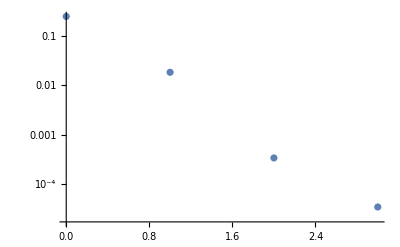

```mathematica
ListLogPlot[zZNlist]
```

```mathematica
(*airy:*)
aABJM[kk_]:=If[EvenQ[kk],
-Zeta[3]/(π^2*kk)-2/kk*Sum[m*(kk/2-m)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk/2-1}],
-Zeta[3]/(8*π^2*kk)+kk/4*Log[2]-1/kk*Sum[(kk+(-1)^m*(2*m-kk))/4*(kk-(kk+(-1)^m*(2*m-kk))/4)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk-1}]
];
aA=1/2*(aABJM[6*k]+9*aABJM[2*k]);
cC=1/(3*π^2*k);
(*B should be shifted by k*(some quadratic polynomial of M/k)*)
bB=(π^2*cC)/3-5/(18*k)+k/4;
logZpert=Table[{nN,Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)]},{nN,0,nmax+1,0.01}];
```

```mathematica
range={{0,nmax+1},All};
imsize=400;
plot1=ListLogPlot[{zZNlist,logZpert,zZNlist},Joined->{False,True,False},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]]},PlotMarkers->{{"●",10},"",{"●",10}},PlotRange->range,Frame->True,FrameLabel->{"N","Z_(2, 1)(N)"},PlotLegends->Placed[{"Z_(2, 1)(N)","e^AC^(-1/3)Ai[C^(-1/3)(N-B)]"},{0.75,0.8}],ImageSize->imsize]
```

-Graphics-

```mathematica
(**)
(*I suspect that the values of partition functions Subscript[Z, 2,1](N) are still wrong for the following two reasons:*)
(**)
(*1. I expect the phase of the partition function is trival (real positive), or at most Exp[(π*I)/k*(some simple polynomial in M,N,k with rational coefficients)], which is anyway e^(πi(rational)).*)
(*    But the phase of Subscript[Z, 2,1](2) does not fit with this form.*)
(**)
(*2. I expect log[Subscript[Z, k,M](N)] coincides, up to O(e^(-(...)√N)) corrections, with Airy with the same coefficients A,C and with B shifted by k*(some quadratic polynomial in M/k). Here the shift should be a quadratic polynomial if there is a Hanany-Witten duality under M -> (...)k-(...)M.*)
(*    Anyway the plot of Subscript[Z, k,M](N) and the Airy curve must coincides under an appropriate parallel transport in N corresponding to the ambiguity in B.*)
(*    But this seems not be the case.*)
(**) 
(**)
```